## Systems

```mathematica
mg[tend_,param_]:=Module[{tdelay=2,init={x[0]==0.5},pars={β->param,γ->1,n->9.65}},
eq={x'[t]==(β x[t-tdelay])/(1+x[t-tdelay]^n)-γ x[t]};
NDSolveValue[{eq/.pars,init},{x},{t,0,tend}]
]
mech[tend_]:=Module[{init={x[0]==0.5,x'[0]==0},pars={ω0->1,q->1,β->1}},
eq={x''[t]==(-ω0/q x'[t]-ω0^2 x[t]-β x[t]^3)};
NDSolveValue[{eq/.pars,init},{x},{t,0,tend}]
]
```

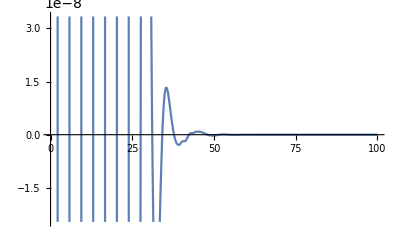

```mathematica
Plot[mech[100][[1]][y],{y,0,100},PlotRange->Automatic]
```

## Reservoir Characteristics

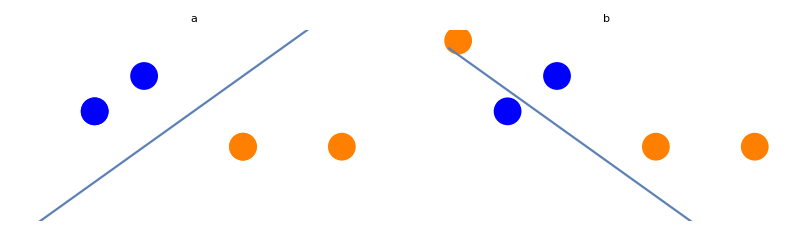

-Graphics3D-

```mathematica
classificationData1={{{1,2},{0.5,1.5}},{{3,1},{2,1}}};
g1=Show[ListPlot[classificationData1,PlotStyle->{Directive[Blue,PointSize[0.05]],Directive[Orange,PointSize[0.05]]},PlotLabel->Style["a",Black,Bold],PlotRange->{{-0.1,3.1},{0,2.6}},Axes->False],Plot[t,{t,-0.1,3.1}]];
classificationData2={{{1,2},{0.5,1.5}},{{3,1},{2,1},{0,2.5}}};
g2=Show[ListPlot[classificationData2,PlotStyle->{Directive[Blue,PointSize[0.05]],Directive[Orange,PointSize[0.05]]},PlotLabel->Style["b",Black,Bold],PlotRange->{{-0.1,3.1},{0,2.6}},Axes->False],Plot[-t+2.3,{t,-0.1,3.1}]];
classificationData3={{{1,2,3},{0.5,1.5,2}},{{3,1,0},{2,1,1},{0,2.5,0}}};
GraphicsGrid[{{g1,g2}},Frame->All]
g3=Show[ListPointPlot3D[classificationData3,PlotLabel->Style["c",Black,Bold],Axes->False,Boxed->True,PlotStyle->{Directive[Blue,PointSize[0.02]],Directive[Orange,PointSize[0.02]]},PlotRange->{{-0.1,3.1},{0,3},{-0.1,3.1}}],Plot3D[1.5,{x,0,3},{y,0,3},PlotStyle->Opacity[0.3]]]
```

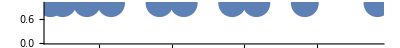

```mathematica
uppedData=Table[{Prime[i],i,-Sin[i]},{i,1,10}];
GraphicsGrid[{{NumberLinePlot[Prime[Range[10]],PlotStyle->{PointSize[0.05]},TicksStyle->Medium]},{ListPointPlot3D[uppedData,PlotStyle->{PointSize[0.05]},TicksStyle->Medium]}},Frame->All]
```

## Mech Bifurcation Plot

```mathematica
sunflowerPars={ω0->ω,ω1->10,q->1,β1->1,β2->0.05,β3->1,A->10,Ω->1000};
Clear[peaks,data,ts,runs]
mech[tend_,ω_]:=Module[{init={x1[0]==0.5,x1'[0]==0,x2[0]==0,x2'[0]==0,x3[0]==0.5,x3'[0]==0.5},pars={ω0->ω,ω1->100,q->1,β1->1,β2->0.05,β3->1,A->100,Ω->1000}},
eq={x1''[t]==(-ω0/q x1'[t]-ω0^2 x1[t]-β1 x1[t]^3)+A(1+u[t])Cos[Ω t]+ω1^2(x2[t]-x1[t]),x2''[t]==(-ω0/q x2'[t]-ω0^2 x2[t]-β2 x2[t]^3)+A(1+u[t])Cos[Ω t]+ω1^2(x1[t]-2x2[t]+x3[t]),x3''[t]==(-ω0/q x3'[t]-ω0^2 x3[t]-β3 x3[t]^3)+A(1+u[t])Cos[Ω t]+ω1^2(x2[t]-x3[t]),u[t]==SawtoothWave[t]};
NDSolveValue[{eq/.pars,init},{x1,x2,x3},{t,0,tend}]
]
roundPeaks[ts_,tolerance_]:=Module[{},
Table[Round[ts[[i]],tolerance],{i,1,Length@ts}]//DeleteDuplicates
]
coarsePeakQ[ts_,j_,g_]:=Module[{},
If[(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#<ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#<ts[[j]]&])||(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#>ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#>ts[[j]]&]),ts[[j]],0]
]
finePeakQ[ts_,j_,g_]:=Module[{},
If[(ts[[j-1]]<ts[[j]]&&ts[[j+1]]<ts[[j]])||(ts[[j-1]]>ts[[j]]&&ts[[j+1]]>ts[[j]]),ts[[j]],0]
]
getPeaks[data_,tolerance_:0.02,granularity_:1]:=Module[{ts=If[ListQ[data],data,Table[data[x],{x,0,30,0.1}]],peaks={}},
Monitor[For[i=3,i<Length@ts-3,i++,
AppendTo[peaks,finePeakQ[ts,i,granularity]]
],i];
roundPeaks[peaks//DeleteCases[0],tolerance]
]
bifurcationData[startG_,endG_,inc_]:=Module[{runs=Table[{i,mech[30,i][[1]]},{i,startG,endG,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startG-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
```

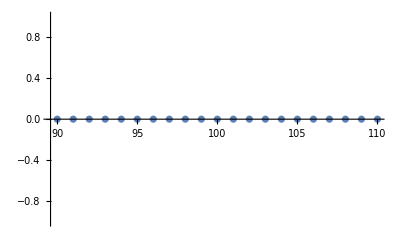

```mathematica
ListPlot[bifurcationData[90,110,1]]//Quiet
```

```mathematica
mechPlot=mech[30,1];
```

NDSolveValue::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolveValue::reinitfail: Unable to reinitialize the system at t = 30. within specified tolerances.

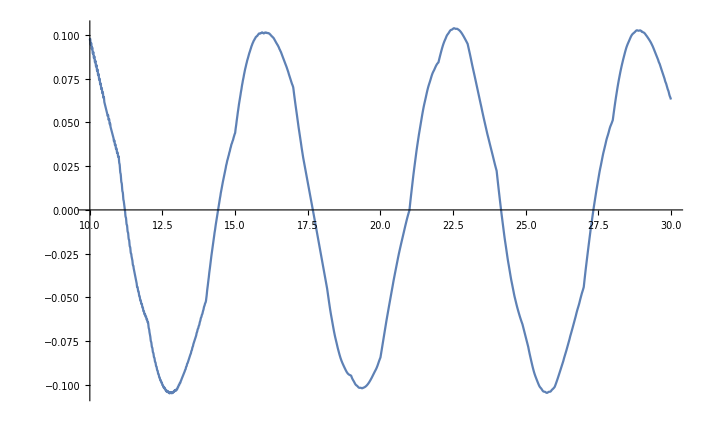

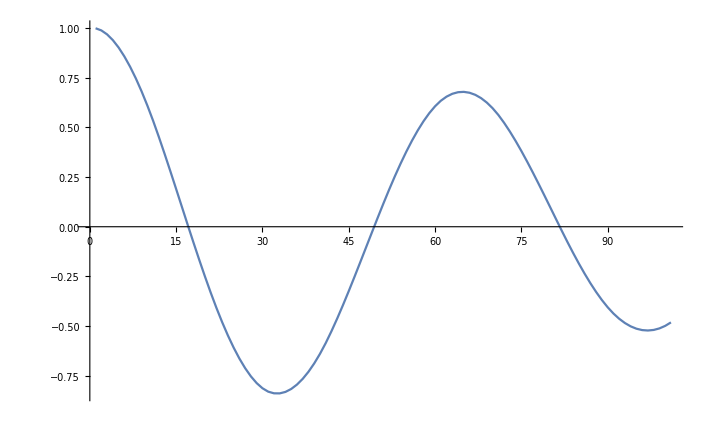

-Graphics3D-

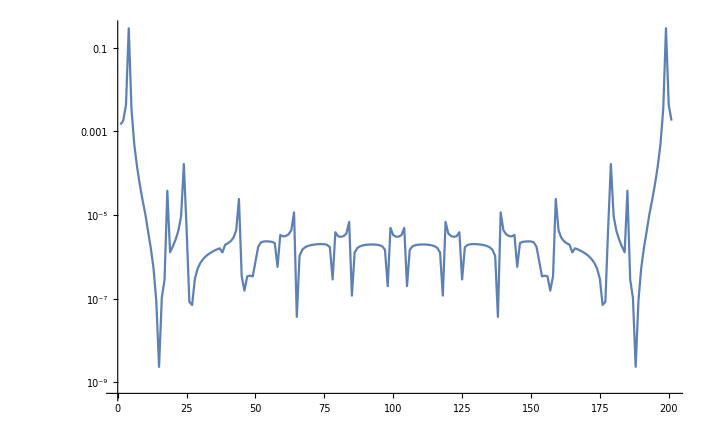

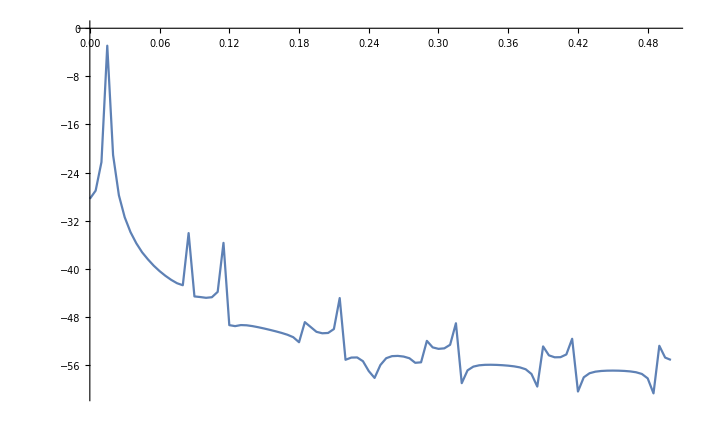

```mathematica
mechList=Table[mechPlot[[1]][x],{x,10,30,0.1}];
Plot[mechPlot[[1]][x],{x,10,30}]
ListPlot[CorrelationFunction[mechList,{100}],Joined->True]
ListPointPlot3D[Table[{mechList[[i]],mechList[[i-6]],mechList[[i-12]]},{i,12,200}]]
mechFftp=Fourier[mechList];
ListLogPlot[Table[Re[mechFftp[[i]]]^2,{i,1,Length@mechFftp}],PlotRange->{All,All},Joined->True]
Periodogram[mechList]
```

```mathematica
elephantAn=Table[ParametricPlot3D[{mechPlot[[1]][t],mechPlot[[1]][t-1],mechPlot[[1]][t-2]},{t,5,a},PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.1,0.1}},Axes->False,ImageSize->Large],{a,6,21,0.01}];
```

```mathematica
ParametricPlot3D[{mechPlot[[1]][t],mechPlot[[1]][t-1],mechPlot[[1]][t-2]},{t,15,16}]
```

-Graphics3D-

## More Mech Bifurcation Plot

```mathematica
Clear[peaks,data,ts,runs]
mech[tend_,ω_]:=Module[{init={x1[0]==0.5,x1'[0]==0,x2[0]==0,x2'[0]==0,x3[0]==0.5,x3'[0]==0.5},pars={ω0->ω,ω1->1.5,q->60,β1->1,β2->0.05,β3->1,β4->0.05,A->0.8,Ω->1.14}},
eq={x1''[t]==(-ω0/q x1'[t]-ω0^2 x1[t]-β1 x1[t]^3)+A(1)Cos[Ω t]+ω1^2(x2[t]-x1[t]),x2''[t]==(-ω0/q x2'[t]-ω0^2 x2[t]-β2 x2[t]^3)+A(1+0.7u[t])Cos[Ω t]+ω1^2(x1[t]-2x2[t]+x3[t]),x3''[t]==(-ω0/q x3'[t]-ω0^2 x3[t]-β3 x3[t]^3)+A(1+0.7u[t])Cos[Ω t]+ω1^2(x2[t]-2x3[t]+x4[t]),x4''[t]==(-ω0/q x4'[t]-ω0^2 x4[t]-β4 x4[t]^3)+A(1)Cos[Ω t]+ω1^2(x3[t]-x4[t]),u[t]==Sin[0.2t]};
NDSolveValue[{eq/.pars,init},{x1,x2,x3},{t,0,tend}]
]
roundPeaks[ts_,tolerance_]:=Module[{},
Table[Round[ts[[i]],tolerance],{i,1,Length@ts}]//DeleteDuplicates
]
coarsePeakQ[ts_,j_,g_]:=Module[{},
If[(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#<ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#<ts[[j]]&])||(AllTrue[Table[ts[[k]],{k,j-g,j-1}],#>ts[[j]]&]&&AllTrue[Table[ts[[k]],{k,j+1,j+g}],#>ts[[j]]&]),ts[[j]],0]
]
finePeakQ[ts_,j_,g_]:=Module[{},
If[(ts[[j-1]]<ts[[j]]&&ts[[j+1]]<ts[[j]])||(ts[[j-1]]>ts[[j]]&&ts[[j+1]]>ts[[j]]),ts[[j]],0]
]
getPeaks[data_,tolerance_:0.02,granularity_:1]:=Module[{ts=If[ListQ[data],data,Table[data[x],{x,0,100,0.1}]],peaks={}},
Monitor[For[i=3,i<Length@ts-3,i++,
AppendTo[peaks,coarsePeakQ[ts,i,granularity]]
],i];
roundPeaks[peaks//DeleteCases[0],tolerance]
]
bifurcationData[startG_,endG_,inc_]:=Module[{runs=Table[{i,mech[100,i][[1]]},{i,startG,endG,inc}]},
peaks=Table[getPeaks[runs[[i,2]]],{i,1,Length@runs}];
Flatten[Table[Table[{(n+startG-1)*inc,peaks[[n,m]]},{m,1,Length@peaks[[n]]}],{n,1,Length@peaks}],1]
]
```

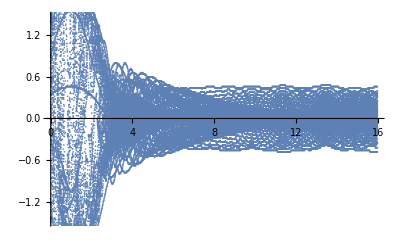

```mathematica
ListPlot[bifurcationData[-1.0,15,0.01]]//Quiet
```

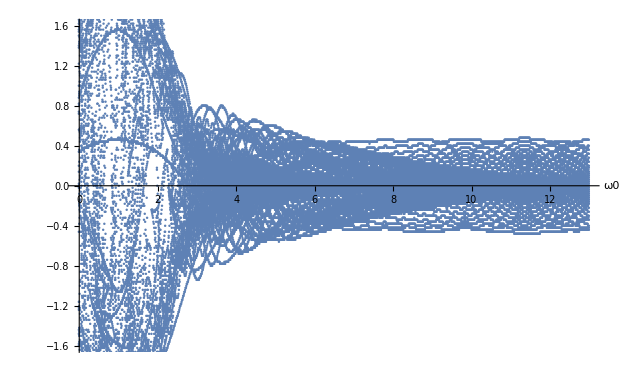

```mathematica
ListPlot[bifurcationData[-1.0,12,0.01],AxesLabel->{Style["ω0",Bold,Larger],""}]//Quiet
```

```mathematica
mechPlot=mech[100,1.3];
```

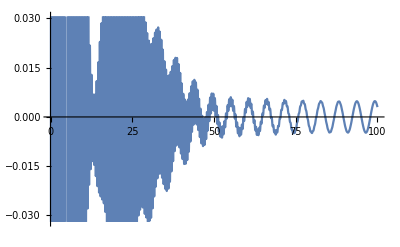

```mathematica
mechPlot2=mech[100,13][[1]];
Plot[mechPlot2[x],{x,0,100}]
```

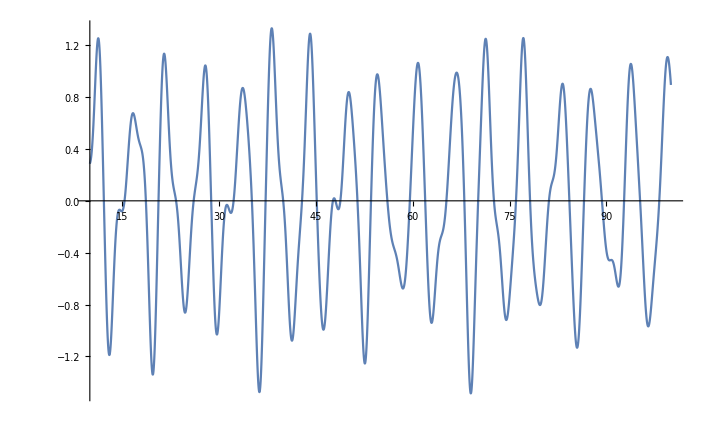

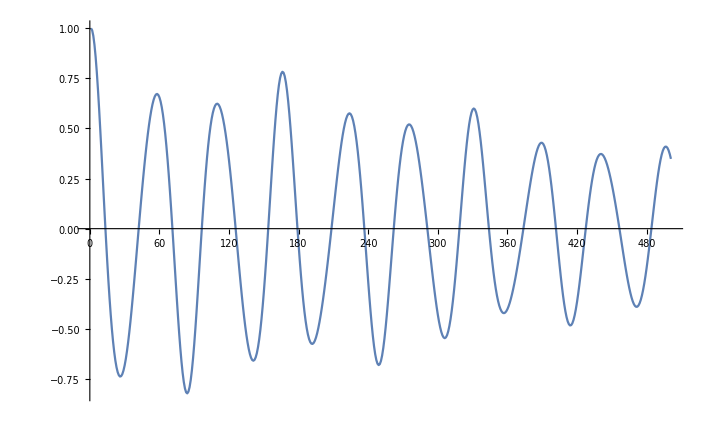

-Graphics3D-

-Graphics3D-

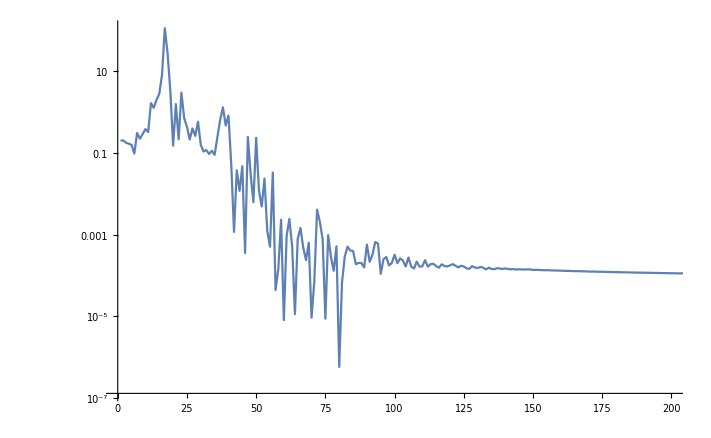

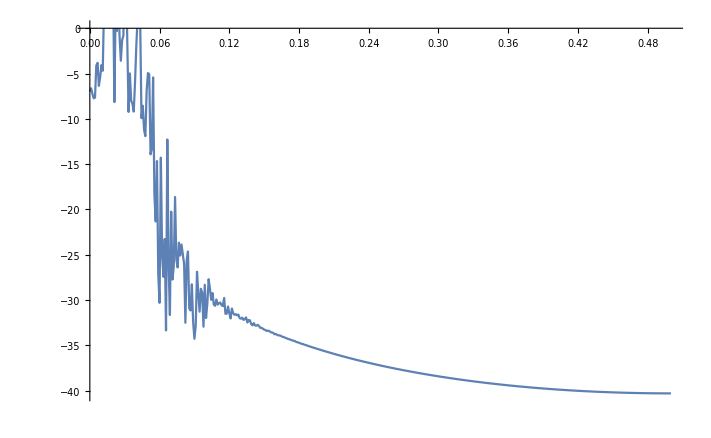

```mathematica
mechList=Table[mechPlot[[1]][x],{x,10,100,0.1}];
Plot[mechPlot[[1]][x],{x,10,100}]
ListPlot[CorrelationFunction[mechList,{500}],Joined->True]
ListPointPlot3D[Table[{mechList[[i]],mechList[[i-6]],mechList[[i-12]]},{i,12,900}],AxesLabel->{Style["x[t]",Bold,Larger],Style["x[t-τ]",Bold,Larger],Style["x[t-2τ]",Bold,Larger]}]
ListPointPlot3D[Table[{mechList[[i]],mechList[[i-25]],mechList[[i-50]]},{i,50,900}]]
mechFftp=Fourier[mechList];
ListLogPlot[Table[Re[mechFftp[[i]]]^2,{i,1,Length@mechFftp}],PlotRange->{{0,200},All},Joined->True]
Periodogram[mechList]
```

```mathematica
ParametricPlot3D[{mechPlot[[1]][t],mechPlot[[1]][t-1],mechPlot[[1]][t-2]},{t,10,90}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t]+Sin[2t],Sin[t-1]+Sin[2t-2],Sin[t-2]+Sin[2t-4]},{t,10,90}]
```

-Graphics3D-

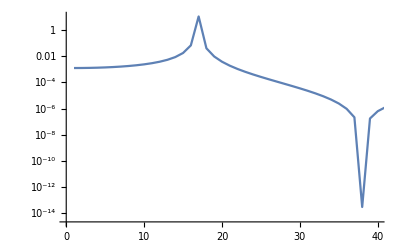

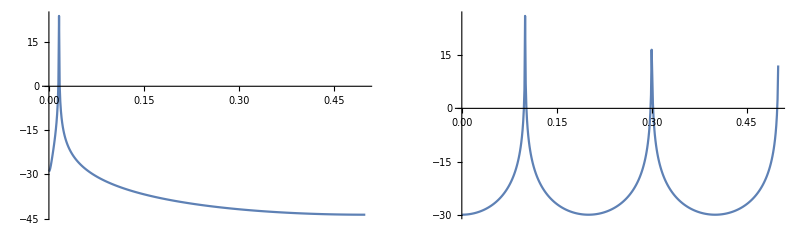

```mathematica
sinList=Table[Sin[i],{i,0,100,0.1}];
squareList=Table[SquareWave[i],{i,0,100,0.1}];
sinFftp=Fourier[sinList];
ListLogPlot[Table[Re[sinFftp[[i]]]^2,{i,1,Length@sinFftp}],PlotRange->{{0,40},All},Joined->True]
GraphicsGrid[{{Periodogram[sinList,PlotRange->Full],
Periodogram[squareList,PlotRange->Full]}}]
```

## Mech Animations

```mathematica
harmOsc[tend_,ω_]:=Module[{init={x[0]==1,x'[0]==0},pars={ω0->ω}},
eq={x''[t]==-ω0^2 x[t]};
NDSolveValue[{eq/.pars,init},{x},{t,0,tend}]
]
stiffSoftOsc[tend_,βIn_]:=Module[{init={x[0]==1,x'[0]==0},pars={ω0->1,β->βIn}},
eq={x''[t]==-ω0^2 x[t]-β x[t]^3};
NDSolveValue[{eq/.pars,init},{x},{t,0,tend}]
]
dampedOsc[tend_,pIn_]:=Module[{init={x[0]==1,x'[0]==0},pars={ω0->1,β->5,p->pIn}},
eq={x''[t]==-p x'[t]-ω0^2 x[t]-β x[t]^3};
NDSolveValue[{eq/.pars,init},{x},{t,0,tend}]
]
drivenOsc[tend_,AIn_,ΩIn_]:=Module[{init={x[0]==1,x'[0]==0},pars={ω0->1,β->5,p->0.5,A->AIn,Ω->ΩIn}},
eq={x''[t]==-p x'[t]-ω0^2 x[t]-β x[t]^3+A Cos[Ω t]};
NDSolveValue[{eq/.pars,init},{x},{t,0,tend}]
]
mech[tend_,ω_]:=Module[{init={x1[0]==0.5,x1'[0]==0,x2[0]==0,x2'[0]==0,x3[0]==0.5,x3'[0]==0.5},pars={ω0->ω,ω1->1.5,q->60,β1->1,β2->0.05,β3->1,β4->0.05,A->0.8,Ω->1.14}},
eq={x1''[t]==(-ω0/q x1'[t]-ω0^2 x1[t]-β1 x1[t]^3)+A(1)Cos[Ω t]+ω1^2(x2[t]-x1[t]),x2''[t]==(-ω0/q x2'[t]-ω0^2 x2[t]-β2 x2[t]^3)+A(1+0.7u[t])Cos[Ω t]+ω1^2(x1[t]-2x2[t]+x3[t]),x3''[t]==(-ω0/q x3'[t]-ω0^2 x3[t]-β3 x3[t]^3)+A(1+0.7u[t])Cos[Ω t]+ω1^2(x2[t]-2x3[t]+x4[t]),x4''[t]==(-ω0/q x4'[t]-ω0^2 x4[t]-β4 x4[t]^3)+A(1)Cos[Ω t]+ω1^2(x3[t]-x4[t]),u[t]==Sin[0.2t]};
NDSolveValue[{eq/.pars,init},{x1,x2,x3},{t,0,tend}]
]
```

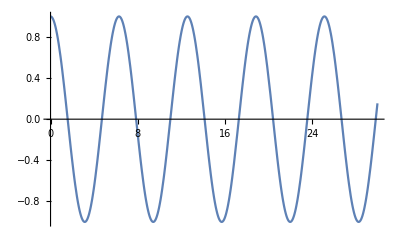

```mathematica
ho=harmOsc[30,1][[1]];
hoAn=Animate[Plot[ho[x],{x,0,a},PlotRange->{{0,30},{-1,1}},PlotLabel->Style["x''(t) = -ω0^2 x(t)",Black,18]],{a,1,30},AnimationRunning->False,AnimationRate->.75]
```

```mathematica
sso=stiffSoftOsc[30,10][[1]];
ssoAn=Animate[Plot[sso[x],{x,0,a},PlotRange->{{0,30},{-1,1}},PlotLabel->Style["x''(t) = -ω0^2x(t) - βx^3(t)",Black,18]],{a,1,30},AnimationRunning->False,AnimationRate->.75]
```

```mathematica
doOver=dampedOsc[30,10][[1]];
doUnder=dampedOsc[30,0.1][[1]];
doOverAn=Animate[Plot[doOver[x],{x,0,a},PlotRange->{{0,30},{-1,1}},PlotLabel->Style["x''(t) = -ω0/Qx'(t) - ω0^2x(t) - βx^3(t)",Black,18]],{a,1,30},AnimationRunning->False,AnimationRate->.75]
doUnderAn=Animate[Plot[doUnder[x],{x,0,a},PlotRange->{{0,30},{-1,1}},PlotLabel->Style["x''(t) = -ω0/Qx'(t) - ω0^2x(t) - βx^3(t)",Black,18]],{a,1,30},AnimationRunning->False,AnimationRate->.75]
```

```mathematica
doMatch=drivenOsc[30,10,1][[1]];
doFast=drivenOsc[30,10,10][[1]];
doMatchAn=Animate[Plot[doMatch[x],{x,0,a},PlotRange->{{0,30},{-2,2}},PlotLabel->Style["x''(t) = -ω0/Qx'(t) - ω0^2x(t) - βx^3(t) + A cos(Ωt)",Black,16]],{a,1,30},AnimationRunning->False,AnimationRate->.75]
doFastAn=Animate[Plot[doFast[x],{x,0,a},PlotRange->{{0,30},{-2,2}},PlotLabel->Style["x''(t) = -ω0/Qx'(t) - ω0^2x(t) - βx^3(t) + A cos(Ωt)",Black,16]],{a,1,30},AnimationRunning->False,AnimationRate->.75]
```

```mathematica
co=mech[30,1.3];
co1=co[[1]];
co2=co[[2]];
co3=co[[3]];
coAn=Animate[Show[Plot[co1[x],{x,0,a},PlotRange->{{0,30},{-2,2}},PlotLabel->Style["x_i''(t) = -ω0/Qx_i'(t) - ω0^2x_i(t) - βx_i^3(t) + A cos(Ωt) + ω1^2[x_(i - 1)(t)-2x_i(t)+x_(i + 1)(t)]",Black,10]],Plot[co2[x],{x,0,a},PlotStyle->{Red}],Plot[co3[x],{x,0,a},PlotStyle->{Green}]],{a,1,30},AnimationRunning->False,AnimationRate->.75]
```

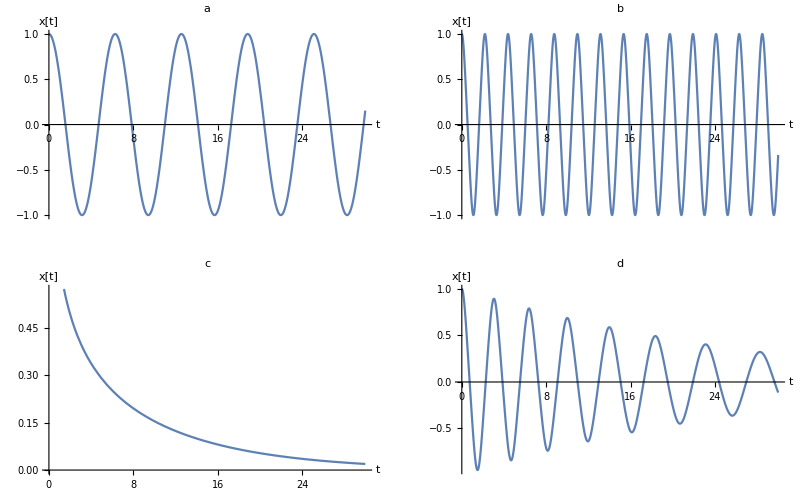

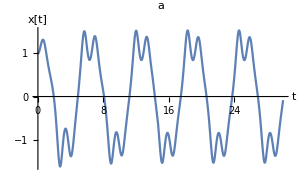
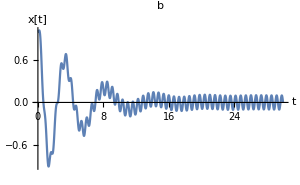
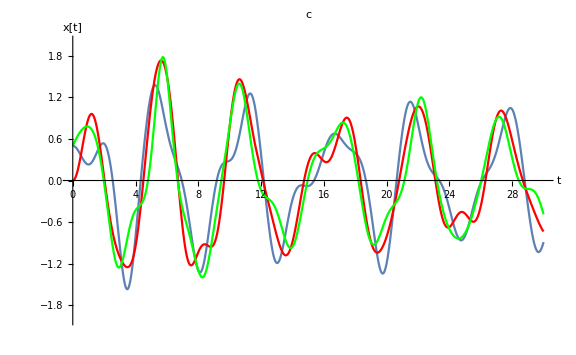

```mathematica
hoPlot=Plot[ho[x],{x,0,30},PlotLabel->Style["a",Black,12],AxesLabel->{"t","x[t]"}];
ssoPlot=Plot[sso[x],{x,0,30},PlotLabel->Style["b",Black,12],AxesLabel->{"t","x[t]"}];
doOverPlot=Plot[doOver[x],{x,0,30},PlotLabel->Style["c",Black,12],AxesLabel->{"t","x[t]"}];
doUnderPlot=Plot[doUnder[x],{x,0,30},PlotLabel->Style["d",Black,12],AxesLabel->{"t","x[t]"}];
doMatchPlot=Plot[doMatch[x],{x,0,30},PlotLabel->Style["a",Black,12],ImageSize->300,AxesLabel->{"t","x[t]"}];
doFastPlot=Plot[doFast[x],{x,0,30},PlotLabel->Style["b",Black,12],ImageSize->300,AxesLabel->{"t","x[t]"},PlotRange->Full];
coPlot=Show[Plot[co1[x],{x,0,30},PlotRange->{{0,30},{-2,2}},PlotLabel->Style["c",Black,12],AxesLabel->{"t","x[t]"}],Plot[co2[x],{x,0,30},PlotStyle->{Red}],Plot[co3[x],{x,0,30},PlotStyle->{Green}],ImageSize->Large];
GraphicsGrid[{{hoPlot,ssoPlot},{doOverPlot,doUnderPlot}}]
Column[Row[#,Spacer[5]]&/@{{doMatchPlot,doFastPlot},{coPlot}},Alignment->Center]
```

### Exports

```mathematica
Export["D:\\W21\\COMPS\\hoAn.avi",hoAn,AnimationDuration->30]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

D:\W21\COMPS\hoAn.avi

```mathematica
Export["D:\\W21\\COMPS\\ssoAn.avi",ssoAn,AnimationDuration->30]
```

D:\W21\COMPS\ssoAn.avi

```mathematica
Export["D:\\W21\\COMPS\\doOverAn.avi",doOverAn,AnimationDuration->30]
```

D:\W21\COMPS\doOverAn.avi

```mathematica
Export["D:\\W21\\COMPS\\doUnderAn.avi",doUnderAn,AnimationDuration->30]
```

$Aborted

```mathematica
Export["D:\\W21\\COMPS\\doMatchAn.avi",doMatchAn,AnimationDuration->30]
```

D:\W21\COMPS\doMatchAn.avi

```mathematica
Export["D:\\W21\\COMPS\\doFastAn.avi",doFastAn,AnimationDuration->30]
```

D:\W21\COMPS\doFastAn.avi

```mathematica
Export["D:\\W21\\COMPS\\coAn.avi",coAn,AnimationDuration->30]
```

D:\W21\COMPS\coAn.avi

## Quantum Reservoir

```mathematica
Needs["QuantumUtils`"]
Needs["QUTesting`"];
RunAllTests[]
```

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyTrueQ found; using a blank message instead.

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyFalseQ found; using a blank message instead.

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyNonzeroQ found; using a blank message instead.

General::stop: Further output of AssignUsage::nousg will be suppressed during this calculation.

Needs::string: String expected at position 2 in Needs[PredicatesTests`,FileNameJoin[{QUDevTools`Private`TestingPath,PredicatesTests.m}]].

Needs::string: String expected at position 2 in Needs[TensorTests`,FileNameJoin[{QUDevTools`Private`TestingPath,TensorTests.m}]].

Needs::string: String expected at position 2 in Needs[QuantumSystemsTests`,FileNameJoin[{QUDevTools`Private`TestingPath,QuantumSystemsTests.m}]].

General::stop: Further output of Needs::string will be suppressed during this calculation.

0 of 7 unit tests passed.

```mathematica
tf1=Import["D:\\W21\\COMPS\\TreeFractal1.PNG"];
tf2=Import["D:\\W21\\COMPS\\TreeFractal2.PNG"];
tf3=Import["D:\\W21\\COMPS\\TreeFractal3.PNG"];
GraphicsGrid[{{tf1,tf2,tf3}}]
```

-Graphics-